```mathematica
Quit[];
```

```mathematica
$FeynRulesPath = SetDirectory["/Users/noahsteinberg/Library/Mathematica/Applications/feynrules-current"];
FR$Parallel=False;
<<FeynRules`;
SetDirectory["/Users/noahsteinberg/Library/Mathematica/Applications/feynrules-current/Models/RealSinglet"];
LoadModel["SMSinglet.fr"]
```

- FeynRules -

Version: 2.3.32 ( 12 March 2018).

Authors: A. Alloul, N. Christensen, C. Degrande, C. Duhr, B. Fuks

Please cite:

- Comput.Phys.Commun.185:2250-2300,2014 (arXiv:1310.1921);

- Comput.Phys.Commun.180:1614-1641,2009 (arXiv:0806.4194).

http://feynrules.phys.ucl.ac.be

The FeynRules palette can be opened using the command FRPalette[].

args::shdw: Symbol args appears in multiple contexts {FeynRules`,Global`}; definitions in context FeynRules` may shadow or be shadowed by other definitions.

This model implementation was created by

N. Steinberg

Model Version: 1.0

For more information, type ModelInformation[].

- Loading particle classes.

- Loading gauge group classes.

- Loading parameter classes.

Model Singlet Extension loaded.

```mathematica
LoadRestriction["DiagonalCKM.rst", "Massless.rst"]
```

Loading restrictions from DiagonalCKM.rst :  / 3

Loading restrictions from Massless.rst :  / 18

Restrictions loaded.

```mathematica
WriteUFO[LSM];
```

--- Universal FeynRules Output (UFO) v 1.1 ---

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

130 possible non-zero vertices have been found -> starting the computation:  / 130.

125 vertices obtained.

Flavor expansion of the vertices:  / 125

- Saved vertices in InterfaceRun[ 1 ].

Computing the squared matrix elements relevant for the 1->2 decays:

/ 47

Squared matrix elent compute in 1.04303 seconds.

Decay::Overwrite: Warning: Previous results will be overwritten.

Decay widths computed in 0.067605 seconds.

Preparing Python output.

- Splitting vertices into building blocks.

- Optimizing: /151 .

- Writing files.

Done!

```mathematica
fullvers = FeynmanRules[LSM];
```

Starting Feynman rule calculation.

Expanding the Lagrangian...

Collecting the different structures that enter the vertex.

130 possible non-zero vertices have been found -> starting the computation:  / 130.

125 vertices obtained.

```mathematica
decays=ComputeWidths[fullvers];
```

Flavor expansion of the vertices:  / 125

Computing the squared matrix elements relevant for the 1->2 decays:

/ 47

```mathematica
Hhh[tanb_,mheavy_,alph_]:=  decays[[1]][[2]]/.lam-> (Mh*Cos[alpha])^2/(2*vev^2)+(MH*Sin[alpha])^2/(2*vev^2)/.lam2->(Mh*Sin[alpha])^2/(2*svev^2)+(MH*Cos[alpha])^2/(2*svev^2)/.lam3-> (MH^2-Mh^2)*2*Cos[alpha]*Sin[alpha]/(2*svev*vev)/.svev->(vev/tanbeta)/.alpha->alph/.Mh->125/.vev->246/.MZ->91/.MW-> 80/.cw->80/91/.sw->Sqrt[1-(80/91)^2]/.ee-> Sqrt[4π(1/137)]/.MB-> 4.18/.yb->Sqrt[2]*4.18/246/.MT-> 172/.yt->Sqrt[2]*172/246/.MTA->1.776/.ytau->Sqrt[2]*1.776/246/.tanbeta->tanb/.MH->mheavy;
Hbb[tanb_,mheavy_,alph_]:=  decays[[6]][[2]]/.lam-> (Mh*Cos[alpha])^2/(2*vev^2)+(MH*Sin[alpha])^2/(2*vev^2)/.lam2->(Mh*Sin[alpha])^2/(2*svev^2)+(MH*Cos[alpha])^2/(2*svev^2)/.lam3-> (MH^2-Mh^2)*2*Cos[alpha]*Sin[alpha]/(2*svev*vev)/.svev->(vev/tanbeta)/.alpha->alph /.Mh->125/.vev->246/.MZ->91/.MW-> 80/.cw->80/91/.sw->Sqrt[1-(80/91)^2]/.ee-> Sqrt[4π(1/137)]/.MB-> 4.18/.yb->Sqrt[2]*4.18/246/.MT-> 172/.yt->Sqrt[2]*172/246/.MTA->1.776/.ytau->Sqrt[2]*1.776/246/.tanbeta->tanb/.MH->mheavy;
Htautau[tanb_,mheavy_,alph_]:=   decays[[7]][[2]]/.lam-> (Mh*Cos[alpha])^2/(2*vev^2)+(MH*Sin[alpha])^2/(2*vev^2)/.lam2->(Mh*Sin[alpha])^2/(2*svev^2)+(MH*Cos[alpha])^2/(2*svev^2)/.lam3-> (MH^2-Mh^2)*2*Cos[alpha]*Sin[alpha]/(2*svev*vev)/.svev->(vev/tanbeta)/.alpha->alph/.Mh->125/.vev->246/.MZ->91/.MW-> 80/.cw->80/91/.sw->Sqrt[1-(80/91)^2]/.ee-> Sqrt[4π(1/137)]/.MB-> 4.18/.yb->Sqrt[2]*4.18/246/.MT-> 172/.yt->Sqrt[2]*172/246/.MTA->1.776/.ytau->Sqrt[2]*1.776/246/.tanbeta->tanb/.MH->mheavy;
Htt[tanb_,mheavy_,alph_]:=   decays[[8]][[2]]/.lam-> (Mh*Cos[alpha])^2/(2*vev^2)+(MH*Sin[alpha])^2/(2*vev^2)/.lam2->(Mh*Sin[alpha])^2/(2*svev^2)+(MH*Cos[alpha])^2/(2*svev^2)/.lam3-> (MH^2-Mh^2)*2*Cos[alpha]*Sin[alpha]/(2*svev*vev)/.svev->(vev/tanbeta)/.alpha->alph/.Mh->125/.vev->246/.MZ->91/.MW-> 80/.cw->80/91/.sw->Sqrt[1-(80/91)^2]/.ee-> Sqrt[4π(1/137)]/.MB-> 4.18/.yb->Sqrt[2]*4.18/246/.MT-> 172/.yt->Sqrt[2]*172/246/.MTA->1.776/.ytau->Sqrt[2]*1.776/246/.tanbeta->tanb/.MH->mheavy;
Hww [tanb_,mheavy_,alph_]:=   decays[[10]][[2]]/.lam-> (Mh*Cos[alpha])^2/(2*vev^2)+(MH*Sin[alpha])^2/(2*vev^2)/.lam2->(Mh*Sin[alpha])^2/(2*svev^2)+(MH*Cos[alpha])^2/(2*svev^2)/.lam3-> (MH^2-Mh^2)*2*Cos[alpha]*Sin[alpha]/(2*svev*vev)/.svev->(vev/tanbeta)/.alpha->alph/.Mh->125/.vev->246/.MZ->91/.MW-> 80/.cw->80/91/.sw->Sqrt[1-(80/91)^2]/.ee-> Sqrt[4π(1/137)]/.MB-> 4.18/.yb->Sqrt[2]*4.18/246/.MT-> 172/.yt->Sqrt[2]*172/246/.MTA->1.776/.ytau->Sqrt[2]*1.776/246/.tanbeta->tanb/.MH->mheavy;
Hzz[tanb_,mheavy_,alph_]:=   decays[[13]][[2]]/.lam-> (Mh*Cos[alpha])^2/(2*vev^2)+(MH*Sin[alpha])^2/(2*vev^2)/.lam2->(Mh*Sin[alpha])^2/(2*svev^2)+(MH*Cos[alpha])^2/(2*svev^2)/.lam3-> (MH^2-Mh^2)*2*Cos[alpha]*Sin[alpha]/(2*svev*vev)/.svev->(vev/tanbeta)/.alpha->alph/.Mh->125/.vev->246/.MZ->91/.MW-> 80/.cw->80/91/.sw->Sqrt[1-(80/91)^2]/.ee-> Sqrt[4π(1/137)]/.MB-> 4.18/.yb->Sqrt[2]*4.18/246/.MT-> 172/.yt->Sqrt[2]*172/246/.MTA->1.776/.ytau->Sqrt[2]*1.776/246/.tanbeta->tanb/.MH->mheavy;
Totalheavywidth[tanb_,mheavy_,alph_] = Hhh[tanb,mheavy,alph] + Hbb[tanb,mheavy,alph] + Htautau[tanb,mheavy,alph] +Htt[tanb,mheavy,alph] +  Hww [tanb,mheavy,alph] + Hzz[tanb,mheavy,alph] ;
```

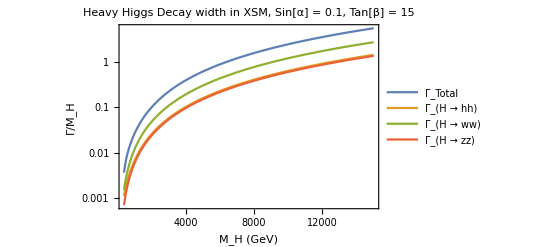

```mathematica
LogPlot[{Totalheavywidth[0.1,x,.2]/x,Hhh[0.1,x,.2]/x,Hww[0.1,x,.2]/x,Hzz[0.1,x,.2]/x(*,Htt[1,x,.2],Hbb[1,x,.2],Htautau[1,x,.2]*)},{x,400,15000},Frame->True,PlotLegends->{"Γ_Total","Γ_(H → hh)","Γ_(H → ww)","Γ_(H → zz)","Γ_(H → tt)","Γ_(H → bb)","Γ_(H → ττ)"},PlotLabel->"Heavy Higgs Decay width in XSM, Sin[α] = 0.1, Tan[β] = 15",FrameLabel->{"M_H (GeV)","Γ/M_H"}]
```

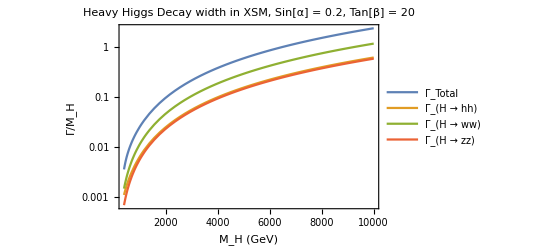

```mathematica
LogPlot[{Totalheavywidth[0.1,x,.2]/x,Hhh[0.1,x,.2]/x,Hww[0.1,x,.2]/x,Hzz[0.1,x,.2]/x(*,Htt[1,x,.1],Hbb[1,x,.1],Htautau[1,x,.1]*)},{x,400,10000},Frame->True,PlotLegends->{"Γ_Total","Γ_(H → hh)","Γ_(H → ww)","Γ_(H → zz)","Γ_(H → tt)","Γ_(H → bb)","Γ_(H → ττ)"},PlotLabel->"Heavy Higgs Decay width in XSM, Sin[α] = 0.2, Tan[β] = 20",FrameLabel->{"M_H (GeV)","Γ/M_H"}]
```

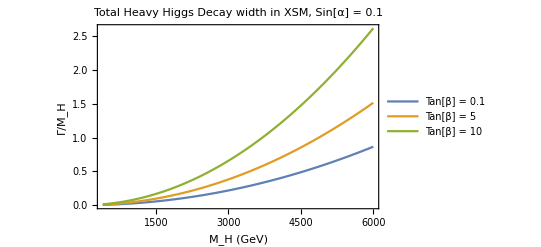

```mathematica
Plot[{Totalheavywidth[0.1,x,.2]/x,Totalheavywidth[5,x,.2]/x,Totalheavywidth[10,x,.2]/x},{x,400,6000},Frame->True,PlotLegends->{"Tan[β] = 0.1","Tan[β] = 5","Tan[β] = 10"},PlotLabel->"Total Heavy Higgs Decay width in XSM, Sin[α] = 0.1",FrameLabel->{"M_H (GeV)","Γ/M_H"}]
```

```mathematica
λ1[tb_,α_,heavy_]:= (Mh*Cos[alpha])^2/(2*vev^2)+(MH*Sin[alpha])^2/(2*vev^2)/.Mh->125/.vev->246/.MZ->91/.MW-> 80/.cw->80/91/.sw->Sqrt[1-(80/91)^2]/.ee-> Sqrt[4π(1/137)]/.Cos[alpha]->Sqrt[1-Sin[alpha]^2]/.tanbeta->tb/.alpha->α/.MH->heavy;
λ2[tb_,α_,heavy_]:= (Mh*Sin[alpha])^2/(2*svev^2)+(MH*Cos[alpha])^2/(2*svev^2)/.svev->(vev/tanbeta)/.Mh->125/.vev->246/.MZ->91/.MW-> 80/.cw->80/91/.sw->Sqrt[1-(80/91)^2]/.ee-> Sqrt[4π(1/137)]/.Cos[alpha]->Sqrt[1-Sin[alpha]^2]/.tanbeta->tb/.alpha->α/.MH->heavy;
λ3[tb_,α_,heavy_]:= (MH^2-Mh^2)*2*Cos[alpha]*Sin[alpha]/(2*svev*vev)/.svev->(vev/tanbeta)/.Mh->125/.vev->246/.MZ->91/.MW-> 80/.cw->80/91/.sw->Sqrt[1-(80/91)^2]/.ee-> Sqrt[4π(1/137)]/.Cos[alpha]->Sqrt[1-Sin[alpha]^2]/.tanbeta->tb/.alpha->α/.MH->heavy;
```

```mathematica
one = LogLogPlot[{λ1[Subscript[t, β],.2,1000],λ2[Subscript[t, β],.2,1000],λ3[Subscript[t, β],.2,1000]},{Subscript[t, β],0.1,50},Frame->True,PlotLabel-> "λ_i vs Tan[β] for Sin[α] = 0.2",FrameLabel->{"Tan[β]","λ_i"},PlotLegends->{"λ_1(M_H = 1TeV)","λ_2(M_H = 1TeV)","λ_3(M_H = 1TeV)"}];
two = LogLogPlot[{λ1[Subscript[t, β],.2,2000],λ2[Subscript[t, β],.2,2000],λ3[Subscript[t, β],.2,2000]},{Subscript[t, β],0.1,50},Frame->True,PlotLabel-> "λ_i vs Tan[β] for Sin[α] = 0.2",FrameLabel->{"Tan[β]","λ_i"},PlotLegends->{"λ_1(M_H = 2TeV)","λ_2(M_H = 2TeV)","λ_3(M_H = 2TeV)"},PlotStyle->Dashed];
five = LogLogPlot[{λ1[Subscript[t, β],.2,5000],λ2[Subscript[t, β],.2,5000],λ3[Subscript[t, β],.2,5000]},{Subscript[t, β],0.1,50},Frame->True,PlotLabel-> "λ_i vs Tan[β] for Sin[α] = 0.2",FrameLabel->{"Tan[β]","λ_i"},PlotLegends->{"λ_1(M_H = 5TeV)","λ_2(M_H = 5TeV)","λ_3(M_H = 5TeV)"},PlotStyle->Dotted];
line = LogLogPlot[4π, {x,0.1,50},Frame->True,PlotStyle->Black];
```

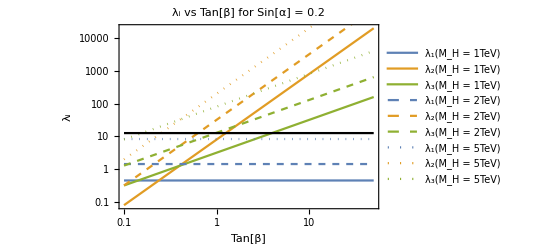

```mathematica
Show[one,two,five,line]
```

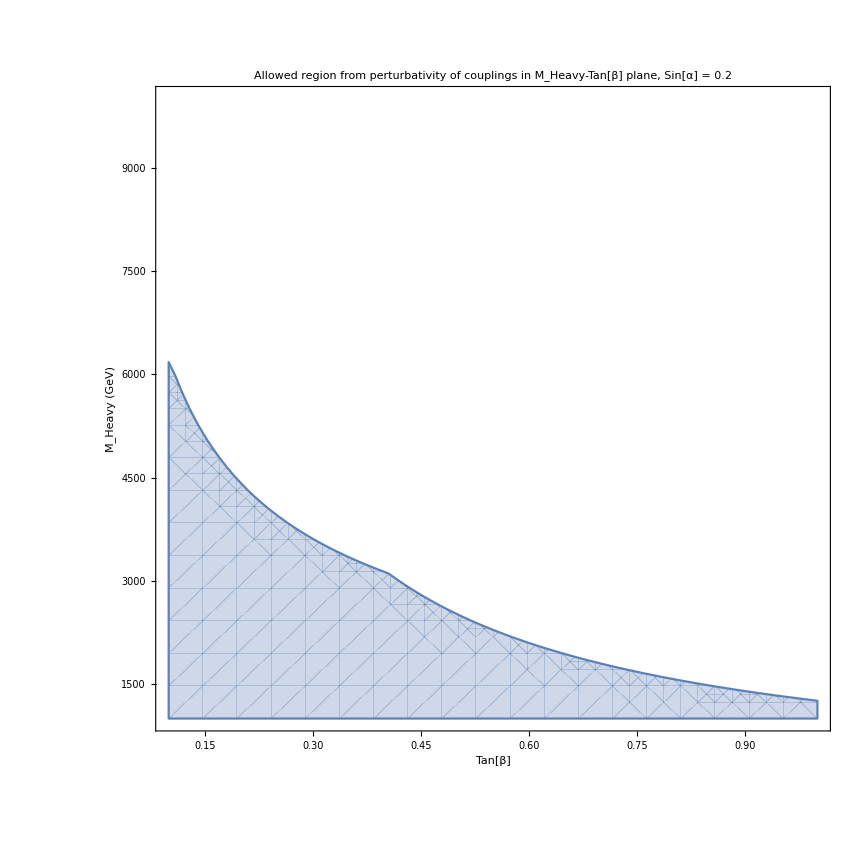

```mathematica
RegionPlot[λ3[tb,.2,MH] < 4π && λ2[tb,.2,MH] < 4π && λ1[tb,.2,MH]<4π, {tb,0.1,1},{MH,1000,10000},Frame->True,FrameLabel->{"Tan[β]","M_Heavy (GeV)"}, PlotLabel->"Allowed region from perturbativity of couplings in M_Heavy-Tan[β] plane, Sin[α] = 0.2"]
```

```mathematica
Subscript[m, h]^2(1 - Sin[α]^2) + Subscript[m, H]^2 Sin[α]^2 < 8 π/□
```

```mathematica
B = 1/6 λ3[tb,α,Subscript[m, H]]/λ1[tb,α,Subscript[m, H]];
A = λ2[tb,α,Subscript[m, H]]/λ1[tb,α,Subscript[m, H]];
```

```mathematica
1/6 λ3[1,0.2,5000]/λ1[1,0.2,5000]
```

1.61874

((15625 Sin[α]^2)/(121032 tb^2)+((1-Sin[α]^2) m_H^2)/(121032 tb^2))/((15625 (1-Sin[α]^2))/121032+(Sin[α]^2 m_H^2)/121032)

```mathematica
(λ^3 - (A+2)λ^2 + (2*A - B^2 + 3/4)λ - (3/4*A - 5/4 B^2))/.α->.2/.Subscript[m, H]-> 5000
```

-14.7036/tb^2+(3/4+45.3237/tb^2) λ-(2+23.972/tb^2) λ^2+λ^3

```mathematica
Solve[-14.70363672928473/1^2+(3/4+45.32374751543705) λ-(2+23.972027237149476/1^2) λ^2+λ^3 == 0]
```

{{λ→0.414385},{λ→1.47328},{λ→24.0844}}

```mathematica
Solve[(λ^3 - (A+2)λ^2 + (2*A - B^2 + 3/4)λ - (3/4*A - 5/4 B^2)) == 0]
```

Solve::incnst: Inconsistent or redundant transcendental equation. After reduction, the bad equation is -1+2 ArcSin[Sin[α]]^2 == 0.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{α→-1/(√2),λ→1/2,m_H→-125},{α→1/(√2),λ→1/2,m_H→-125},{α→-1/(√2),λ→1/2,m_H→125},{α→1/(√2),λ→1/2,m_H→125},{α→-1/(√2),λ→3/2,m_H→-125},{α→1/(√2),λ→3/2,m_H→-125},{α→-1/(√2),λ→3/2,m_H→125},{α→1/(√2),λ→3/2,m_H→125}}